I took my double well code, plugged in numbers that correspond to the trotsky experiment, and just added that superexchange stuff at the bottom.  The comparsion to their experiment looks good (i might be off by a little on the scattering length), so I'm confident this is correct.

### constants and units

```mathematica
μB=9.27400915*10^-28;
kb=1.380658*10^-23;
ℏ=6.62606896*10^-34(2π)^-1;
c=299792458;
a0 = .529*10^-10;
ϵ0 = 8.854*10^-12;
el = 1.602*10^-19;
AMU=1.66*10^-27*kg;
cm=10^-2;mm=10^-3;μm=10^-6;nm = 10^-9;pm=10^-12;fm=10^-15;
kg=1;g=10^-3;ng=10^-9*g;pg=10^-12*g;
Hz=1;kHz=10^3;MHz=10^6;GHz=10^9; THz = 10^12;
Kk=1;mK=10^-3;μK=10^-6;nK=10^-9;
Ww=1;mW=10^-3;μW=10^-6;nW=10^-9;
Pa=1;GPa=10^9;
ms=10^-3;
ohm=1;V=1;mV=10^-3;
ns = 10^-9;
```

```mathematica
Γ=2*π*5.9*MHz;
λ0:=852nm; λ1=795*nm; λ2=780 *nm;
ω0=2*π*c/λ0;ω1=2*π*c/λ1;ω2=2*π*c/λ2;
mass=87*AMU;ωres = ω2;
```

```mathematica
2MHz*.0001
```

200.

## Numbers

```mathematica
ℏ=1.05457*10^-34;
λ=852.0*10^-9;
ks=(2π)/λ; (*wavevector for the short lattice*)
kl=π/λ; (*wavevector for the long lattice*)
a=λ/2;  (*short lattice spacing*)
amu=1.6605*10^-27;
mRb=86.909*amu;  (*mass or Rb87*)
Er=(ℏ^2 ks^2)/(2mRb); (*Recoil energy of the short lattice*)
as=5.3*10^-9;   (*approximate s-wave scattering length for Rb87 (in meters)*)
```

```mathematica
Er/(2π*ℏ)
```

3162.59

```mathematica
ℏ^2/(mRb*waist^2*2*π*ℏ)
```

206.761

```mathematica
mRb
```

1.44312×10^-25

## For the double gaussian thing

```mathematica
2^14
```

16384

-20.8886-38.3939 Cos[x]-29.4689 Cos[2 x]-18.0389 Cos[3 x]-7.46092 Cos[4 x]+3.75951 Cos[6 x]+4.58024 Cos[7 x]+3.77035 Cos[8 x]+2.47525 Cos[9 x]+1.35717 Cos[10 x]+0.628489 Cos[11 x]+0.243074 Cos[12 x]+0.0749763 Cos[13 x]+0.0156259 Cos[14 x]-0.00199923 Cos[16 x]-0.00122733 Cos[17 x]-0.000509087 Cos[18 x]-0.00016841 Cos[19 x]-0.000046529 Cos[20 x]-0.0000108574 Cos[21 x]-2.11595×10^-6 Cos[22 x]-3.28875×10^-7 Cos[23 x]-3.45376×10^-8 Cos[24 x]+1.12199×10^-9 Cos[26 x]+3.47075×10^-10 Cos[27 x]+7.25429×10^-11 Cos[28 x]+1.20923×10^-11 Cos[29 x]+1.68349×10^-12 Cos[30 x]+1.97956×10^-13 Cos[31 x]+1.94367×10^-14 Cos[32 x]+1.5461×10^-15 Cos[33 x]+5.5218×10^-17 Cos[34 x]

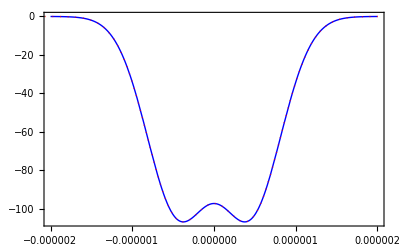

```mathematica
K=100;  (*I would keep the cutoff at least this high*)
λ=852.0*10^-9;
ks=(2π)/λ;
Er=N[(ℏ^2 ks^2)/(2mRb)];
E0=100;
btwn=.9*10^-6;
waist=.75*10^-6;


(*this shit is a mess, but the basic idea is first find a reasonably range to fit the potential over (xrange), then scale this range to be from -π to π in order to generate a fourier series, and then scale it back to real units.
The final result is the functino FAscaled, which is the fourier series approx to your actual potential in SI units*)
Potential[x_]=-E0(Exp[-2((x+btwn/2)/waist)^2]+Exp[-2((x-btwn/2)/waist)^2]);
minR=FindMinimum[Potential[x],{x,.5*10^-6}][[2,1,2]];
minL=-minR;
BV=(Potential[minR]+2(Potential[0]-Potential[minR]));
xrange=(*FindRoot[Potential[x]==BV,{x,2minR}][[1,2]]*11;*) 6*waist;
P0=Plot[Potential[x],{x,-2*10^-6,2*10^-6},PlotStyle->{Thick,Blue},Frame->True];

scale=π/xrange;
btwnscale=scale*btwn;
waistscale=scale*waist;
Potentialscale[x_]=-E0(Exp[-2((x+btwnscale/2)/waistscale)^2]+Exp[-2((x-btwnscale/2)/waistscale)^2]);
FA[x_]=FourierCosSeries[Potentialscale[x],x,K];
P1=Plot[Potentialscale[x],{x,-π,π},PlotStyle->{Thick,Blue}];
P2=Plot[FA[x],{x,-π,π},PlotStyle->{Red,Thick,Dotted}];
FA[x]
FAscaled[x_]=FA[scale*x];
P3=Plot[FAscaled[x],{x,-xrange,xrange},PlotStyle->{Thick,Red,Dotted},Frame->True,PlotRange->All];

Show[P0,P3,Frame->True]
```

```mathematica
FindMaximum[FAscaled[x],{x,0} ]
```

FindMaximum::fmgz: Encountered a gradient that is effectively zero. The result returned may not be a maximum; it may be a minimum or a saddle point.

{-97.3505,{x→0.}}

```mathematica
FAscaled[x]
```

```mathematica
FA[x]
```

```mathematica
30*((.01)/1.4)^(1/2)
```

2.53546

```mathematica
Potential[x]
```

-100 (ⅇ^(-3.55556×10^12 (-4.5×10^-7+x)^2)+ⅇ^(-3.55556×10^12 (4.5×10^-7+x)^2))

```mathematica
FAGreen[x_]=FourierCosSeries[Potential[x],x,9]
```

SystemException[MemoryAllocationFailure,{FAGreen[x_]=FourierCosSeries[Potential[x],x,9],FourierCosSeries[-100 (ⅇ^(-3.55556×10^12 (-4.5×10^-7+x)^2)+ⅇ^(-3.55556×10^12 (4.5×10^-7+x)^2)),x,9],«104»,Erf[5.923843069016351×10^6+2.7×10^-7 ⅈ]}]

```mathematica
E0*Er/206.761/(2*π*ℏ)
```

1529.59

```mathematica
Er
```

2.09555×10^-30

```mathematica
xrange
```

3.75×10^-6

```mathematica
xrangegreen = 5*waist
```

3.75×10^-6

```mathematica
.75*10^-6/xrange
```

0.2

```mathematica
minR*2
```

7.50515×10^-7

### Calculating hoppings, wave functions, etc...

This is what we talked about, HamK contains matrix elements of the Hamiltonian in a basis of plane waves.

```mathematica
Clear[V]
(*Here, and everywhere below, i've changed everything to be in real units.  Just sort of crossing my fingers that this doesn't cause any problems,
 for instance nonzero numbers being taken as zero by MMA.  Wavefunctions come out normalized, and the values of J and U i get are reasonable, so
it is probably ok...*)

coefflist=Table[Coefficient[Chop[FA[x]],Cos[i x]],{i,1,K}];
HamK=Table[If[i==j,ℏ^2/(2*mRb)((2π)/(2*xrange))^2((K+1)/2-i)^2,.5*Er*coefflist[[Abs[i-j]]]],{i,1,K},{j,1,K}];




egsKK=Eigensystem[N[HamK]];
sysKK=Sort[Table[{egsKK[[1,i]],egsKK[[2,i]]},{i,1,K}]];
RES=Re[Sort[egsKK[[1]]]];
Jlist=Table[(RES[[i+1]]-RES[[i]])/2,{i,1,K-1,2}]; (*Tunnelings in units of recoils*)
(*For the tunneling, it's the splitting between adjacent even and odd eigenstates DIVIDED BY TWO*)
(*This is just because a matrix like {{0,J},{J,0}} has eigenvalues split by 2J*)
```

```mathematica
coefflist[[1]]*.5*Er/(2π*ℏ)
```

-60712.

```mathematica
Er
```

```mathematica
2.0955486306728515*^-30/(2*π*ℏ)
```

3162.59

```mathematica
List::usage
```

{e_1,e_2,…} is a list of elements.

```mathematica
HamK[[1]][[1]]/(2*π*ℏ)
```

69446.

```mathematica
Jlist/Er*(Er/(2π*ℏ))
```

{0.722277,34.6368,592.91,2256.76,3117.38,3646.49,4951.17,8898.1,10528.8,10703.9,9827.55,8264.76,6375.73,4442.22,2608.65,779.493,15.1534,14.4321,11.4049,7.93458,4.94005,2.80319,1.47433,0.728232,0.341092,0.152584,0.0655587,0.0271849,0.0109283,0.00427836,0.00163918,0.000617996,0.000230687,0.0000858279,0.0000320379,0.0000120654,4.59965×10^-6,1.77551×10^-6,6.9182×10^-7,2.70495×10^-7,1.05319×10^-7,4.04609×10^-8,1.52014×10^-8,5.52393×10^-9,1.93718×10^-9,6.2599×10^-10,1.94564×10^-10,5.07559×10^-11,1.69186×10^-11,2.5378×10^-11}

```mathematica
(Er/(2π*ℏ))
```

3162.59

```mathematica
Jlist/(2π*ℏ)
```

{0.722277,34.6368,592.91,2256.76,3117.38,3646.49,4951.17,8898.1,10528.8,10703.9,9827.55,8264.76,6375.73,4442.22,2608.65,779.493,15.1534,14.4321,11.4049,7.93458,4.94005,2.80319,1.47433,0.728232,0.341092,0.152584,0.0655587,0.0271849,0.0109283,0.00427836,0.00163918,0.000617996,0.000230687,0.0000858279,0.0000320379,0.0000120654,4.59965×10^-6,1.77551×10^-6,6.9182×10^-7,2.70495×10^-7,1.05319×10^-7,4.04609×10^-8,1.52014×10^-8,5.52393×10^-9,1.93718×10^-9,6.2599×10^-10,1.94564×10^-10,5.07559×10^-11,1.69186×10^-11,2.5378×10^-11}

```mathematica
FindMinimum[Potential[x],{x,btwn}][[1]]-Potential[0]
```

-9.56159

```mathematica
Er/(2π*ℏ)
```

3162.59

### Tabulating tunneling, 50 recoil depth, 0.55 μm waist vary between

```mathematica
between ={0.62,.6,.65, .7,.75};
bump = {2.22,1.23,4.1,7.8,11.9} ;
j = {1195,2350,327,17,.52};
```

### Tabulating tunneling and bump, .65 spacing, vary depth

```mathematica
depth = {50,25, 15,10,75};
bump = {4.1, 2.05,1.23,.82,6.13};
J={327, 669,899.15,1042,170};
int = {425,252,172,127,576};
```

### Tabulating assisting tunneling overlap, 50 recoil depth .55 μm spacing, 852 counter-prop assisted beams, and periodicity of ~852

```mathematica
between = {.65,.6,.7.75};
JassistCP = {.058,.11,.0013,.00008};
Jassist850 = {.0039,.02,.07,.00013};
```

```mathematica
Clear[egsX]
egsX[x_]=Table[Sum[sysKK[[i,2,k]] 1/(√(2*xrange))ⅇ^(ⅈ ((2π)/(2xrange))((K+1)/2-k) x),{k,1,K}],{i,1,K}];
δcorrect=Table[Arg[egsX[.5*xrange][[i]]],{i,1,K-1}];
egsXcp[x_]=Table[Re[Exp[-ⅈ δcorrect[[i]]]egsX[x][[i]]],{i,1,K-1}];

wp[x_]=Table[(egsXcp[x][[i]]+egsXcp[x][[i+1]])/(√2),{i,1,K-1,2}];
wm[x_]=Table[(egsXcp[x][[i]]-egsXcp[x][[i+1]])/(√2),{i,1,K-1,2}];
wR[x_]=Table[If[Abs[wp[0.001*xrange][[i]]]>Abs[wp[-0.001*xrange][[i]]],wp[x][[i]],wm[x][[i]]],{i,1,(K-1)/2}];
wL[x_]=Table[If[Abs[wp[0.001*xrange][[i]]]<Abs[wp[-0.001*xrange][[i]]],wp[x][[i]],wm[x][[i]]],{i,1,(K-1)/2}];

Plot[{egsXcp[x][[1]],egsXcp[x][[2]]},{x,-xrange,xrange},Frame->True,PlotStyle->{{Thick,Blue},{Thick,Red,Dotted}},FrameLabel->{Style["2kx",22],Style["ϕ_0(x) and ϕ_1(x)",22]},FrameStyle->Directive[Thick,16],ImageSize->500]

Plot[{wL[x][[1]],wL[x][[2]],wL[x][[3]]},{x,-xrange,xrange},Frame->True,PlotStyle->{{Thick,Blue},{Thick,Red},{Thick,Green}},FrameLabel->{Style["2kx",22],Style["ω_(L (1))(x), ω_(L (2))(x), and ω_(L (3))(x)",22]},FrameStyle->Directive[Thick,16],ImageSize->500]
```

$Aborted

$Aborted

```mathematica
g=(4*π*ℏ^2*as)/mRb;
stretch=((2π)/a)*((2π)/a); 
U1=Er^-1*g*stretch*Vxperp*Vyperp*Re[NIntegrate[Abs[wL[x][[1]]]^4,{x,-xrange,xrange}]] (*This is the Hubbard U for the lowest band in units of recoils*)
U2=Er^-1*g*stretch*Vxperp*Vyperp*Re[NIntegrate[Abs[wL[x][[2]]]^4,{x,-xrange,xrange}]] (*This is the Hubbard U for the lowest band in units of recoils*)
U3=Er^-1*g*stretch*Vxperp*Vyperp*Re[NIntegrate[Abs[wL[x][[3]]]^4,{x,-xrange,xrange}]] (*This is the Hubbard U for the lowest band in units of recoils*)
```

0.421359 Vxperp Vyperp

0.30685 Vxperp Vyperp

0.296762 Vxperp Vyperp

```mathematica
(.92)^9
```

0.472161

```mathematica
Exp[-.05/8]^9
```

0.945303

```mathematica
(.86)/1.14^(1/2)
```

0.805464

```mathematica
1-(7.676/10.04)^(1/2)
```

0.125619

```mathematica
1-180/200//N
```

0.1

## Raman assisted tunneling

```mathematica
NIntegrate[Conjugate[wL[x][[1]]]wL[x][[1]], {x,-xrange,xrange}]
```

2.98263×10^-19

```mathematica
wL[xrange][[1]]
```

708.986

```mathematica
Jassis[λraman_] := Norm[NIntegrate[Conjugate[wL[x][[1]]]Exp[2*I*(2 π/(λraman*10^-9)*x)]wR[x][[1]], {x,-xrange,xrange}]];
Jassis[780]
```

0.00249173

```mathematica
Jassis[780]*20000
```

49.8346

```mathematica
RootApproximant[49.834644974021735]
```

Root[37+643 #1+394 #1^2-58 #1^3+#1^4&,4]

```mathematica
(.6/(1.4*20))^(1/2)150
```

21.9578

```mathematica
(2*2π)/(780*10^-9)*18*10^-9*(150/22)^(1/2)//N
```

0.75722

```mathematica
dataTable = Table[{i,Jassis[i]},{i,700,1000,20}];
```

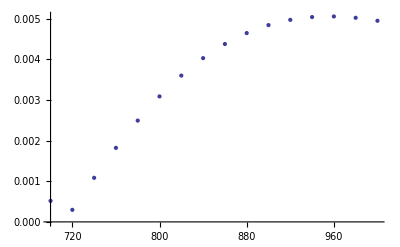

```mathematica
ListPlot[dataTable]
```

```mathematica
xrange
```

```mathematica
FindMaximum[Jassis[λr],{λr,850}]
```

NIntegrate::write: Tag Graphics in  is Protected.

General::stop: Further output of NIntegrate :: write will be suppressed during this calculation.

FindMaximum::nrnum: The function value Norm[NIntegrate[Conjugate[wL[GraphicsBox[Skeleton[9]]] ⟦ 1 ⟧] Exp[ⅈ 2 (2 « 2 » GraphicsBox[Skeleton[9]])] wR[GraphicsBox[List[Skeleton[3]], Rule[Skeleton[2]], Rule[Skeleton[2]], Rule[Skeleton[2]], Rule[Skeleton[2]], Rule[Skeleton[2]], Rule[Skeleton[2]], Rule[Skeleton[2]], Rule[Skeleton[2]]]] ⟦ 1 ⟧, {GraphicsBox[List[List[], List[], List[Compile`$26, Compile`$29]], Rule[AspectRatio, NCache[Power[GoldenRatio, -1], 0.6180339887498948`]], Rule[Axes, True], Rule[AxesLabel, List[None, None]], Rule[AxesOrigin, List[200.`, 0]], Rule[Method, List[]], Rule[PlotRange, List[List[Skeleton[2]], List[Skeleton[2]]]], Rule[PlotRangeClipping, True], Rule[PlotRangePadding, List[Scaled[Skeleton[1]], Automatic]]], -7.648278830690294`*^-7, 7.648278830690294`*^-7}]] is not a real number at {λr} = {850.}.

FindMaximum[Jassis[λr],{λr,850}]

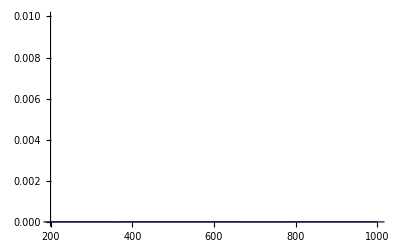

```mathematica
x=Plot[Jassis[λr],{λr,200,1000} , PlotRange-> {0,.01}, PlotStyle-> Thick]
```

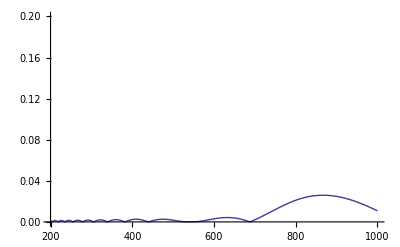
```mathematica
x= -Graphics-
```

-Graphics-

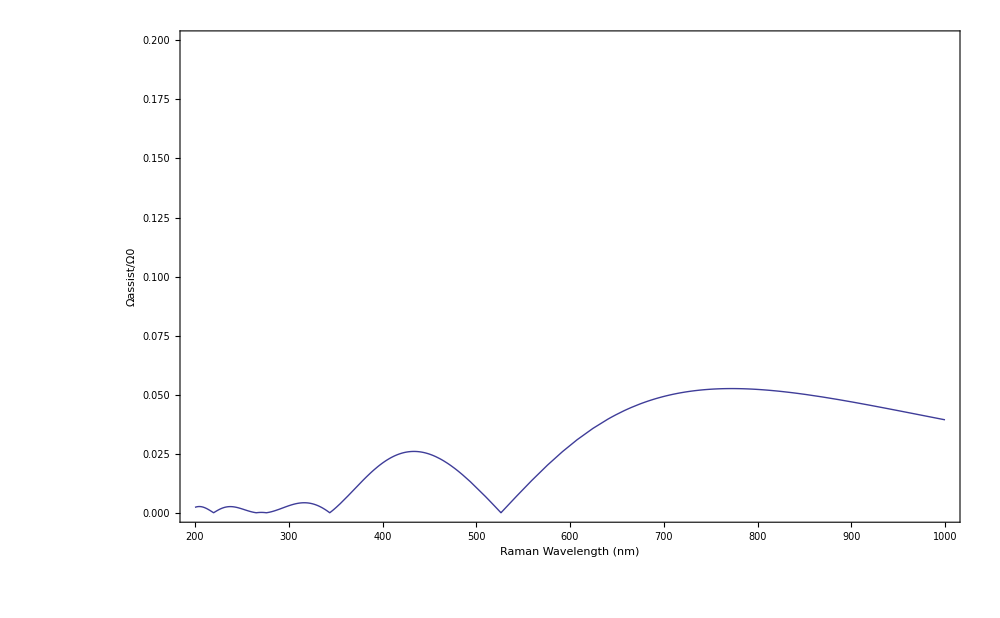

```mathematica
wavePlot  =Show[x, FrameLabel->{"Raman Wavelength (nm)","Ωassist/Ω0"}, Frame-> True, FrameStyle-> Thick, ImageSize-> 1000, LabelStyle-> FontSize->20]
```

```mathematica
Export["/Users/adamkaufman/Desktop/Lab/AMK data and calculations/MMa notebooks/Assisted_tunneling_10Er_.75spot_.95apart_orthogonal.pdf",wavePlot]
```

/Users/adamkaufman/Desktop/Lab/AMK data and calculations/MMa notebooks/Assisted_tunneling_10Er_.75spot_.95apart_orthogonal.pdf

```mathematica
.
```

```mathematica
10kHz*.08
```

800.

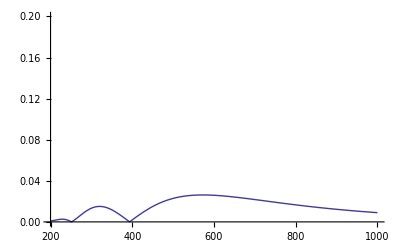

```mathematica
Plot[Jassis[λr],{λr,200,1000} , PlotRange-> {0,.2}]
```

### Playing with known rabi rates

```mathematica
conv = (cons/.Solve[((cons*(.5*10^-3)/(Δ(Δ-FS)))/.{Δ-> -2π*50*10^9, FS-> 2π(c/(780nm)-c/(795nm))})==30*10^3])[[1]]//N
```

8.64799×10^32

```mathematica
Ω[Δ_,P_] = conv*P/(Δ(Δ-FS))/.FS-> 2π(c/(780nm)-c/(795nm));
```

```mathematica
Ω[-2π*50GHz, .5mW]
```

30000.

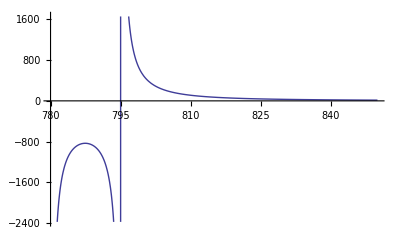

```mathematica
Plot[Ω[-2π*(c/(795nm)-c/(λR*nm)), .5mW], {λR, 780,850}]
```

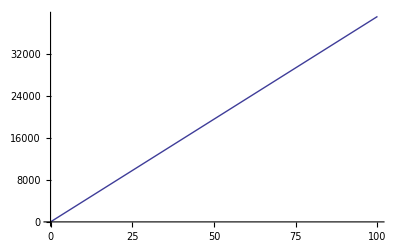

```mathematica
Plot[Ω[-2π*(c/(795nm)-c/(805*nm)), P*mW], {P, 0,100}]
```

```mathematica
GHz
```

1000000000

```mathematica
.35(1/60)^-1//N
```

21.

```mathematica
θx=((15.82-125.6)-(21.5+209.3))/1000
```

-0.34058

```mathematica
θy=((2.01-1260.2)-(4.5-1492.7))/1000
```

0.23001

```mathematica
((.34)^2+(.23)^2)^(1/2)
```

0.410488

```mathematica
.41*π/180*6.35
```

0.0454396

```mathematica
193.5-118.9
```

74.6

```mathematica
392.8-351.8
```

41.

```mathematica
(75^2+41^2)^(1/2)//N
```

85.4751

```mathematica
c
```

299792458

```mathematica
(50GHz)/(c/(795nm)-c/(810*nm)) //N
```

0.00715995

```mathematica
Ω[-2π*(c/(795nm)-c/(810*nm)), .5*mW]/Ω[-2π*50GHz, .5*mW]
```

0.00367267

```mathematica
Γ/(2π)
```

5.9×10^6

### Predicted waist based on measured Rabi rate; checks out with 100 μm

```mathematica
R1i = (2*.1)/(π*rW^2);
i0p = 2.5;
R2i = (2*.08)/(π*rW^2);
i0s = 1.7;
```

```mathematica
Abs[rW/.Solve[2π*30kHz == (Γ^2(R1i/(2*i0p))^(1/2)(R2i/(2*i0s))^(1/2))/(2*2π*50GHz),rW][[1,1]]] cm/μm
```

126.588

## Harmonic approximation of U

```mathematica
(π*w0^2)/(852nm);
```

```mathematica
U
```

-3.25961×10^-26

```mathematica
ωz
```

0.+363160. ⅈ

```mathematica
ΔD2Splitting = 384.2304844685THz;
ΔD1Splitting = 377.107463380 THz;
τD2=26.2348ns;
τD1= 27.679ns;
analyticDepth[λ_, P_, w0r_,ϵ_,mF_,gF_] = (π*c^2 τD2^-1)/(2*(2π*ΔD2Splitting)^3)((2+ϵ*gF*mF)/((c/(λ*nm) -ΔD2Splitting)*2π)+(1-ϵ*gF*mF)/((c/(λ*nm) -ΔD1Splitting)*2π))2*P mW/(π*(w0r*μm)^2);
```

```mathematica
6*.85*.95
```

4.845

```mathematica
m=87AMU;
w0=75μm;
U =-analyticDepth[852,100,50/μm,0,2,1/2];
zR =(π*w0^2)/(852nm);
ωr = ((-4U)/(m*w0^2))^(1/2);
ωz= ((-2U)/(m*zR^2))^(1/2);
ωr/(2π)
ωz/(2π)
ωr/ωz
U/kb
4U/kb
```

1.38066×10^-23

0.+0.000140027 ⅈ

0.+3.58034×10^-7 ⅈ

391.099+0. ⅈ

1.13863×10^-17

4.55454×10^-17

```mathematica
RootApproximant[0.0013799237607936667]
```

(-5410+√29813410)/36354

```mathematica
(1.35/1.39)^(1/2)40
```

39.4203

```mathematica
"convert to exponential"0.+199175.11241499317 ⅈWith[{n=Abs[0.+199175.11241499317 ⅈ],a=Arg[0.+199175.11241499317 ⅈ]},Defer[n ⅇ^(ⅈ a)]]
```

199175. ⅇ^(ⅈ 1.5708)

```mathematica
380/85//N
```

4.47059

```mathematica
.04*π/180.3
```

0.00020944

```mathematica
1/60//N
```

0.0166667

```mathematica
90/12//N
```

7.5

```mathematica
π*(2)^(-1/2)2*1.45μm/(852nm)
```

7.56124

```mathematica
90/20
```

9/2

```mathematica
ψr[n_,x_]:=((√((m ω)/ℏ))^(1/2)1/Sqrt[Sqrt[Pi] 2^n n!] Exp[-((m*ω)/(2*ℏ))x^2] HermiteH[n,(ℏ/(m*ω))^(-1/2)x])/.ω-> ωr;
ψz[n_,x_]:=((√((m ω)/ℏ))^(1/2)1/Sqrt[Sqrt[Pi] 2^n n!] Exp[-((m*ω)/(2*ℏ))x^2] HermiteH[n,(ℏ/(m*ω))^(-1/2)x])/.ω-> ωz;
```

### Interaction

```mathematica
Uint[n_] := (4π*ℏ^2 a)/mass Integrate[ψr[n,x]^4, {x,-∞,∞}]^2 Integrate[ψz[n,x]^4, {x,-∞,∞}]/(2π*ℏ);
```

```mathematica
Uint[0]
```

576.45

```mathematica
(15/60)^2
```

1/16